{1.44618,1.44407}

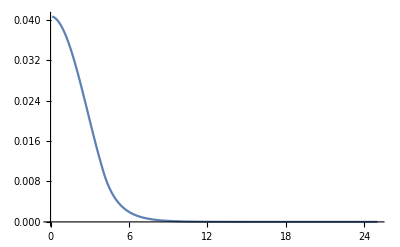

```mathematica
Clear["Global`*"]

NN=201;
rMax=25;
h=rMax/NN;

nMat=1.444;
k0=2Pi/1.55;
l=0;

RIP=Array[(0.0036HeavisideTheta[8.2/2-h#]+1)nMat&,NN];

D1=DiagonalMatrix[ConstantArray[-1/2,NN-1],-1]+DiagonalMatrix[ConstantArray[1/2,NN-1],1];
D1[[1]]=PadRight[{-3/2,2,-1/2},NN];
D1[[-1]]=PadLeft[{1/2,-2,3/2},NN];

D2=Normal[SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{NN,NN}]];
D2[[1]]=PadRight[{2,-5,4,-1},NN];
D2[[-1]]=PadLeft[{-1,4,-5,2},NN];

DivByr=Array[1/h/#&,NN];

{β,Modes}=Eigensystem[D2/h^2+1/h D1 DivByr-l^2DivByr^2 IdentityMatrix[NN]+k0^2 RIP^2 IdentityMatrix[NN]];
β=Sqrt[β];

TrueModesNEff=Chop[Select[β/k0,Re[#]>nMat&] ](*Не самый точный и правильный критерий*)

ListPlot[Abs[Modes[[130]]]^2,PlotRange->All,DataRange->{h,rMax},Joined->True]
```

Домашнее задание
1) Изучить синтаксис операторов: Array, PadRight, PadLeft, SparseArray, Band, Normal, DataRange, Select, PureFunctions
2) Найти коэффициенты Селлмейера для плавленного кварца. Построить кривую показателя преломления по этой формуле и построить кривую материальной ДГС в зависимости от длины волны. 
3) Придумать функцию, которая на вход принимает массив собственных чисел, а на выходе выдает номера физически осмысленных мод (взять критерий отбора из семинара)
4) Численно решить трансцендентное характеристическое уравнение для нахождения собственных мод для ППП - ступеньки (взять данные для волокна SMF28). Найти nEff, построить найденные моды.
5) Импортировать измеренный ППП из файла SMF28.xlsx и симметризовать (придумать как). Найти моды для такого ППП. Пронормировать моды так, чтобы ∫|Ψ|^2ds = 1 (не забыть Якобиан)
6) Придумать свой критерий отсева “мусорных” мод и мод не имеющих физического смысла. Применить к найденному решению задачи 5.